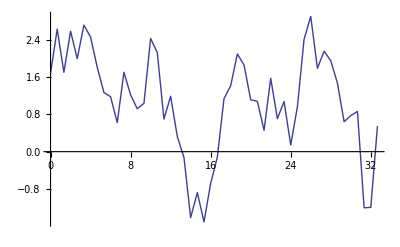

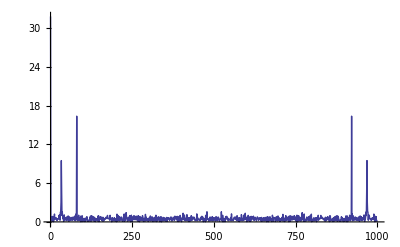

```mathematica
Fs = 1500 (* Hz *);
T=1/Fs; (* Sample time in s *)
NN=1000; (* Number of points *)
t = Range[0,(NN-1)T,T];
x=0.7 Sin[2 Pi 50 t] + Sin[2 Pi 120 t];
y=x+RandomReal[2,NN];
Nplot=50;
f=Transpose[{t[[1;;Nplot]] 1000,y[[1;;Nplot]]}];
ListPlot[f ,Joined->True]
yfft=Fourier[y];
ListPlot[Abs[yfft[[1;;NN]]],Joined->True,PlotRange->All]
```

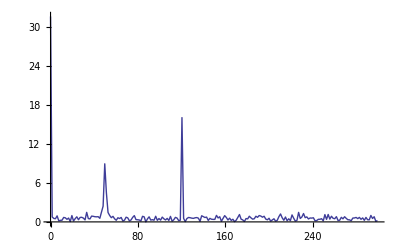

```mathematica
Freqmax=Fs/2;
freq=Freqmax Range[0,1,1/(NN/2-1)];
plotfft=Transpose[{freq,Abs[yfft[[1;;NN/2]]]}];
ListPlot[plotfft[[1;;200]],Joined->True,PlotRange->All]
```

-Graphics-

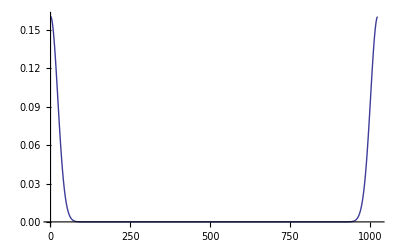

```mathematica
Clear["Global`*"]
NN=2^10;
T=2 10^-12;
T0=10 10^-15;
t=Range[-T/2,T/2,T/(NN-1)];
dt=t[[2]]-t[[1]];
u=Exp[-t^2/(2 T0^2)];
ListPlot[Transpose[{t,u^2}],Joined->True,PlotRange->All]
ufft=Fourier[u];
ListPlot[Abs[ufft]^2,Joined->True,PlotRange->All]
```

```mathematica
freqmax=1/dt /2;
ωspace1=2 Pi freqmax Range[0,1,1/(NN/2-1)];
ωspace2=2 Pi freqmax Range[-1,0, 1/(NN/2-1)];
ωspace = ωspace1 ~Join~ ωspace2;
ListPlot[Transpose[{ωspace,Abs[ufft]^2}],Joined->True,PlotRange->All]
```

-Graphics-

1538.07

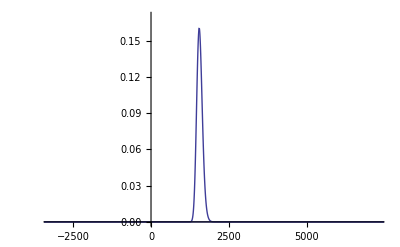

```mathematica
c=3 10^8;
λc=1550 10^-9;
ωc=2 Pi c/λc;
ωspaceshifted=ωspace+ωc;
λspace=2 Pi c / ωspaceshifted;
N[λspace[[4]] 10^9]
ListPlot[Transpose[{λspace 10^9,Abs[ufft]^2}],Joined->True,PlotRange->{0,0.17}]
```